```mathematica
b={-9/16,0,-25/32,-3023/4096,-12551/9600,1282293/163840,-32027856257/722534400,39492614653/412876800}//N
```

{-0.5625,0.,-0.78125,-0.738037,-1.3074,7.8265,-44.3271,95.6523}

```mathematica
ℏc=1.0*^-34*3*^8;
R=2.5*^-6;
func=ℏc/(Pi (L+R))*Sum[b[[i]]*(R/(L+R))^(i+2),{i,1,Length[b]}]//Expand
```

0.+(8.71098×10^-81)/((2.5×10^-6+L)^11)-(1.61473×10^-75)/((2.5×10^-6+L)^10)+(1.1404×10^-70)/((2.5×10^-6+L)^9)-(7.62006×10^-66)/((2.5×10^-6+L)^8)-(1.72064×10^-60)/((2.5×10^-6+L)^7)-(7.28554×10^-55)/((2.5×10^-6+L)^6)-(8.39294×10^-44)/((2.5×10^-6+L)^4)

```mathematica
EPFA=-(Pi^3/720)ℏc*R/L^2
θ1=-1.42;
θ2=2.49;
funcNum=EPFA*(1+θ1*L/R+θ2*L^2/R^2)//Expand
```

-(3.22982×10^-33)/L^2

-1.28676×10^-21-(3.22982×10^-33)/L^2+(1.83454×10^-27)/L

```mathematica
funcMicron=D[func,L]/.L->l*10^(-6)
funcMicronNum=D[funcNum,L]/.L->l*10^(-6)
```

-(9.58207×10^-80)/((2.5×10^-6+l/1000000)^12)+(1.61473×10^-74)/((2.5×10^-6+l/1000000)^11)-(1.02636×10^-69)/((2.5×10^-6+l/1000000)^10)+(6.09605×10^-65)/((2.5×10^-6+l/1000000)^9)+(1.20445×10^-59)/((2.5×10^-6+l/1000000)^8)+(4.37132×10^-54)/((2.5×10^-6+l/1000000)^7)+(3.35717×10^-43)/((2.5×10^-6+l/1000000)^5)

(6.45964×10^-15)/l^3-(1.83454×10^-15)/l^2

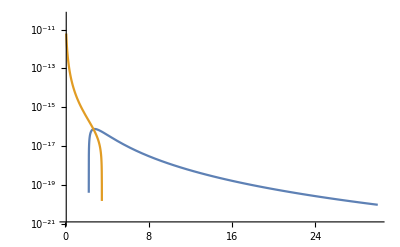

```mathematica
LogPlot[Evaluate@{funcMicron,funcMicronNum},{l,0.1,30}]
near=Table[{l,Evaluate@funcMicronNum*10^18},{l,0.1,0.5,.05}];
far=Table[{l,Evaluate@funcMicron*10^18},{l,10,30}];
nearLog=Table[{Log[l],Evaluate@Log[funcMicronNum*10^18]},{l,0.1,0.5,.1}];
farLog=Table[{Log[l],Evaluate@Log[funcMicron*10^18]},{l,10,30}];
```

```mathematica
near//MatrixForm
far//MatrixForm
```

(0.1 | 6.27619×10^6
0.15 | 1.83243×10^6
0.2 | 761592.
0.25 | 384064.
0.3 | 218862.
0.35 | 135686.
0.4 | 89466.
0.45 | 61828.2
0.5 | 44339.)

(10 | 1.21641
11 | 0.815425
12 | 0.563617
13 | 0.399899
14 | 0.290234
15 | 0.21485
16 | 0.161842
17 | 0.123816
18 | 0.0960455
19 | 0.0754387
20 | 0.0599256
21 | 0.0480937
22 | 0.0389617
23 | 0.0318363
24 | 0.0262209
25 | 0.0217545
26 | 0.0181717
27 | 0.015275
28 | 0.0129156
29 | 0.0109807
30 | 0.0093837)

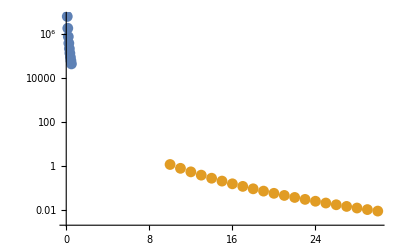

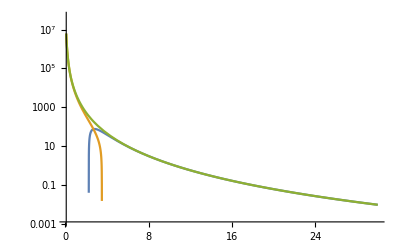

```mathematica
range=Join[nearLog,farLog];
f=Interpolation[range];
ListLogPlot[{near,far}]
LogPlot[Evaluate@{funcMicron*10^18,funcMicronNum*10^18,Exp[f[Log[l]]]},{l,.1,30}]
```

```mathematica
data=Table[{l,Exp[f[Log[l]]]},{l,.1,30,0.01}]
Export[NotebookDirectory[]<>"calculated_exp_vals.tsv",data];
```

{{0.1,6.27619×10^6},{0.11,4.70033×10^6},{0.12,3.60942×10^6},2986,{29.99,0.00939823},{30.,0.0093837}}
 |  |  |  |